# Euler Problem 15

## Lattice Paths

Starting in the top left corner of a 2×2 grid, and only being able to move to the right and down, there are exactly 6 routes to the bottom right corner.

-Graphics-

How many such routes are there through a 20×20 grid?

## Built-in Graph Functions

The built-in Graph functions are too slow to compute this

## Combinatorical Approach

We’re only allowed to move DOWN or RIGHT, consider the following small example:

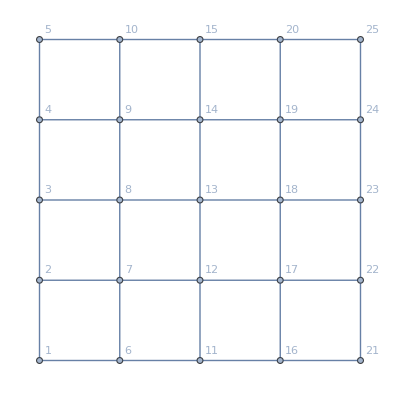
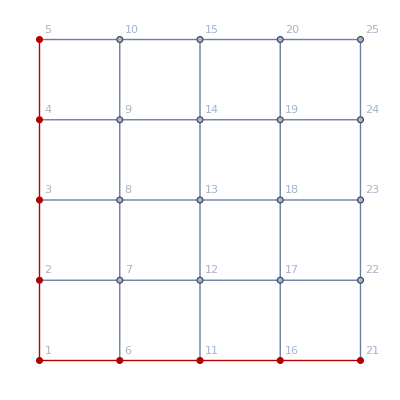

```mathematica
{g5=GridGraph[{5,5},VertexLabels->"Name"],HighlightGraph[g5,PathGraph/@FindPath[g5,5,21,GraphDistance[g5,5,21]]]}
```

This journey is composed of the following:

```mathematica
Table["DOWN",{6}]~Join~Table["RIGHT",{6}]
```

{DOWN,DOWN,DOWN,DOWN,DOWN,DOWN,RIGHT,RIGHT,RIGHT,RIGHT,RIGHT,RIGHT}

How many times can these operations be re-arranged?

```mathematica
(10!)/(5!*5!)
```

252

Function:

```mathematica
fact[1]=1;
fact[2]=2;
fact[n_]:=fact[n]=n*fact[n-1]
```

```mathematica
combinations[gWidth_,gHeight_]:=fact[gWidth+gHeight]/(fact[gWidth] fact[gHeight])
```

```mathematica
combinations[20,20]
```

137846528820